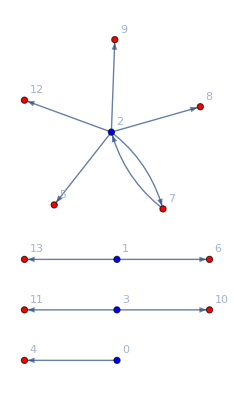

```mathematica
Graph[{0,1,2,3,4,5,6,7,8,9,10,11,12,13},{0->4,2->5,1->6,2->7,2->8,2->9,3->10,3->11,2->12,1->13,7->2},VertexStyle->{0->Blue,1->Blue,2->Blue,3->Blue,4->Red,5->Red,6->Red,7->Red,8->Red,9->Red,10->Red,11->Red,12->Red,13->Red},VertexLabels->"Name"]
```

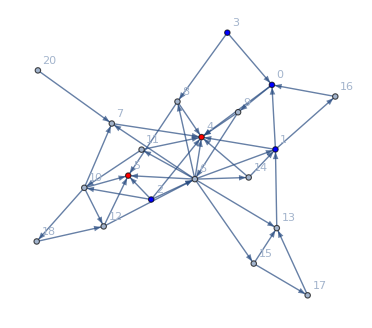

```mathematica
g=Graph[{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18},{0->4,2->5,1->0,1->4,2->6,6->5,6->4,6->7,7->4,8->4,6->8,8->5,3->0,0->9,9->4,2->10,10->5,6->1,6->11,11->4,9->6,10->12,12->5,2->4,3->8,6->13,13->1,20->7,6->14,14->1,6->15,15->13,11->10,1->16,16->0,14->4,12->6,15->17,17->13,10->18,18->12,10->7},VertexStyle->{0->Blue,1->Blue,2->Blue,3->Blue,4->Red,5->Red},VertexLabels->"Name"]
```

```mathematica
Export["NN.png",g ,ImageResolution->300];
```

```mathematica
SystemOpen["NN.png"]
```

```mathematica
SystemOpen["NN.png"]
```

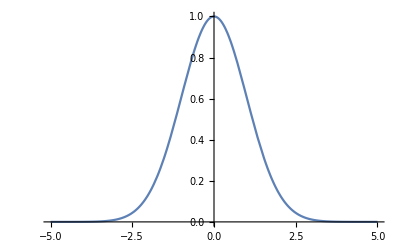

```mathematica
g[x_]:=ⅇ^(-x^2/2);
Plot[g[x],{x,-5,5}]
```